Duffing oscillator: mx’’ - k1 x + k3 x^3=0.  Making the substitutions, x_1=x and x_2=x’, we have:

For m=1, k1=1, k3=1, our system is now:
f1=x2
f2 = x-x^3

{f1,f2} show pitchfork bifurcation.  This is seen in the Euler Buckling problem and more recently in the equation for maximizing wavenumber (wavelength) for long wave instabilities

{x1→-1,x1→0,x1→1}

-x1^2/2+x1^4/4

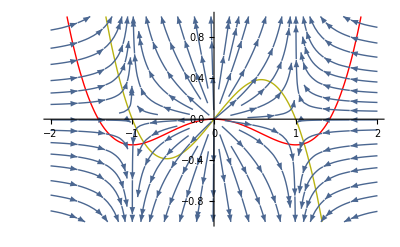

```mathematica
f1=x2;f2=x1-x1^3;
Quiet[Solve[f2==0,x1]]//Flatten
Vx1=-Integrate[f2,x1]
Show[Plot[{f2,Vx1},{x1,-2,2},PlotRange->{All,{-1,1}},PlotStyle->{{Thick,RGBColor[0.72,0.7,0.07]},{Thick,Red}}],
StreamPlot[{f2,f1},{x1,-2,2},{x2,-1,1},StreamStyle->{Thick}]]
```